```mathematica
(* Příklad 1:LED dioda *)
```

```mathematica
(* Priklad 1.1.zluta *)
ClearAll["Global`*"]
u1 =5;
uD = 2;
iD = 20*10^-3;

uR1 = u1-uD
R1 = uR1/iD
```

3

150

```mathematica
(* Priklad 1.1.zelena *)
ClearAll["Global`*"]
u1 =9;
uD = 2.5;
iD = 25*10^-3;

uR1 = u1-uD
R1 = uR1/iD
```

6.5

260.

```mathematica
(* Priklad 1.1.modra *)
ClearAll["Global`*"]
u1 =5;
uD = 3.5;
iD = 30*10^-3;

uR1 = u1-uD
R1 = uR1/iD
```

1.5

50.

```mathematica
(* Priklad 1.2.zluta *)
ClearAll["Global`*"]
R1 =330.;
uD = 2;
iD = 20*10^-3;

uR1 = R1*iD
u1 = uR1+uD
```

6.6

8.6

```mathematica
(* Priklad 1.2.zelena *)
ClearAll["Global`*"]
R1 =220.;
uD = 2.5;
iD = 25*10^-3;

uR1 = R1*iD
u1 = uR1+uD
```

5.5

8.

```mathematica
(* Priklad 1.2.modra*)
ClearAll["Global`*"]
R1 =150.;
uD = 3.5;
iD = 30*10^-3;

uR1 = R1*iD
u1 = uR1+uD
```

4.5

8.

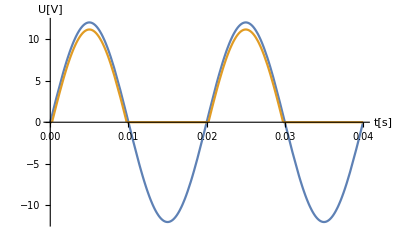

11.1498

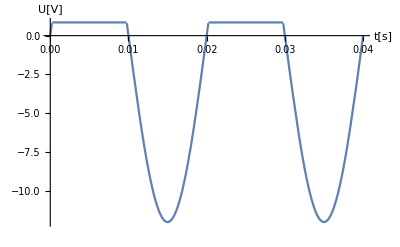

-12.

```mathematica
(* Příklad 2:Jednocestný usměrňovač *)
ClearAll["Global`*"]

rovnice = {
iU[t]+iD1[t]==0,
iD1[t]==iR1[t],
u2[t]==iR1[t]*R1,
iD1[t]==Max[((u1[t]-u2[t])-85/100)*50,0]
};
nezname = { iU[t], iR1[t], iD1[t], u2[t]};

amplituda = 12;
frekvence = 50;
perioda = 1/frekvence;
tmax = 2*perioda;

u1[t_]:=amplituda*Sin[2*π*frekvence*t]

soucastky={R1-> 1000};

reseni = Solve[rovnice/.soucastky,nezname];

resu2  = u2[t]/.reseni;

resu2vyraz = Total[resu2 /.ConditionalExpression[x_,y_] :> Piecewise [{{x,y}}]];

(* ukol 1*)
Plot[{u1[t],resu2vyraz}, {t,0,tmax}, AxesLabel->{"t[s]", "U[V]"}]

(* ukol 2 *)
casMax = 1/4*perioda;
resu2vyraz /. {t-> casMax} //N

(* ukol 3 *)
Plot[{u1[t]-resu2vyraz}, {t,0,tmax}, AxesLabel->{"t[s]", "U[V]"}]
casMaxZaver = 3/4*perioda;
(u1[t]-resu2vyraz)/. {t-> casMaxZaver} //N
```

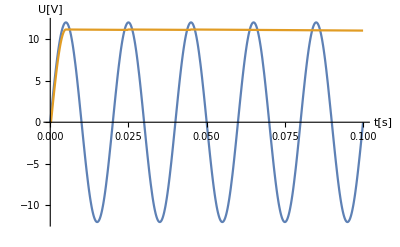

11.1499

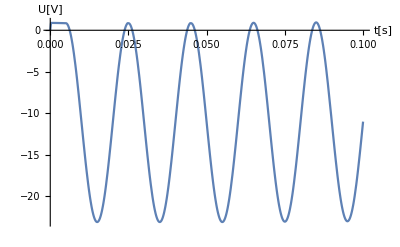

-23.1263

```mathematica
(* Příklad 3:Jednocestný usměrňovač s vyhlazením výstupu*)
ClearAll["Global`*"]

rovnice = {
iU[t]+iD1[t]==0,
iD1[t]==iR1[t]+iC1[t],
u2[t]==iR1[t]*R1,
iD1[t]==Max[((u1[t]-u2[t])-85/100)*50,0],
iC1[t]==C1*u2'[t],
u2[0]==0
};
nezname = { iU[t], iR1[t], iD1[t], u2[t],iC1[t]};

amplituda = 12;
frekvence = 50;
perioda = 1/frekvence;
tmax = 5*perioda;

u1[t_]:=amplituda*Sin[2*π*frekvence*t]

soucastky={R1-> 10000, C1-> 470*10^-6};

reseni = NDSolve[rovnice/.soucastky,nezname, {t,0,tmax}, MaxStepSize->0.001, StartingStepSize->10^-12];

resu2  = u2[t]/.reseni;

resu2vyraz = Total[resu2 /.ConditionalExpression[x_,y_] :> Piecewise [{{x,y}}]];

(* ukol 1*)
Plot[{u1[t],resu2vyraz}, {t,0,tmax}, AxesLabel->{"t[s]", "U[V]"}]

(* ukol 2 *)
casMax = 1/4*perioda;
resu2vyraz /. {t-> casMax} //N

(* ukol 3 *)
Plot[{u1[t]-resu2vyraz}, {t,0,tmax}, AxesLabel->{"t[s]", "U[V]"}]
casMaxZaver = 3/4*perioda;
(u1[t]-resu2vyraz)/. {t-> casMaxZaver} //N
```

```mathematica
(* Operační zesilovače *)
```

```mathematica
(* Příklad 4:invertující zesilovač *)
ClearAll["Global`*"]
rovnice={
iU+iR1==0,
iR2==iR1,
uZ == u1,
u1-u3== iR1*R1,
u3-u2==iR2*R2,
u2==-u3*Aop
};
soucastky={R1-> 1000, R2-> 100*10^3, Aop-> 10^5, uZ-> 50*10^-3};
nezname={
u1, u2, u3,
iR1, iR2,
iU
};

reseni = NSolve[rovnice/.soucastky, nezname]

zesileni = u2/u1/.reseni
```

{{u1→0.05,u2→-4.99496,u3→0.0000499496,iR1→0.0000499501,iR2→0.0000499501,iU→-0.0000499501}}

{-99.8991}

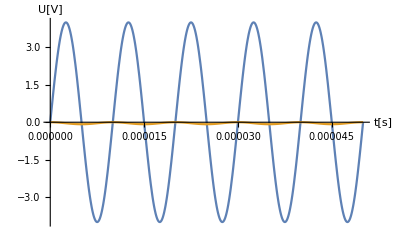

```mathematica
(* Příklad 7:Dolní propust *)
ClearAll["Global`*"]

rovnice = {
iU[t]+iR1[t]==0,
iR1[t]==iC2[t]+iR2[t],
u1[t]-u3[t]==iR1[t]*R1,
u3[t]-u2[t]==iR2[t]*R2,
iC2[t]==C2*(u3'[t]-u2'[t]),
u2[t]==-u3[t]*Aop,
uZ[t]==u1[t],
u2[0]==0,
u3[0]==0
};
frekvence = 100000;
perioda = 1/frekvence;
tmax = 5*perioda;
soucastky = {R1->1000, R2-> 10000, C2-> 160*10^-9,Aop-> 10^5};
uZ[t_]:=4*Sin[2*π*frekvence*t]
nezname={
u1[t],u2[t],u3[t],
iR1[t],iR2[t],
iU[t],
iC2[t]
};

reseni = NDSolve[rovnice/.soucastky, nezname, {t,0,tmax}, Method->{"IndexReduction"->Automatic}, StartingStepSize->10^-12];

Plot[{uZ[t],u2[t]/.reseni},{t,0,tmax},AxesLabel->{"t[s]","U[V]"}]
```

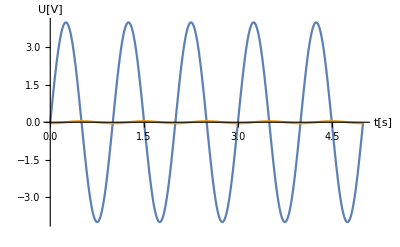

```mathematica
(* Příklad 8:Horní propust *)
ClearAll["Global`*"]

rovnice = {
iU[t]+iC1[t]==0,
iR1[t]==iC1[t],
iR1[t]==iR2[t],
u3[t]-u4[t]==iR1[t]*R1,
u4[t]-u2[t]==iR2[t]*R2,
iC1[t]==C1*(u1'[t]-u3'[t]),
u2[t]==-u4[t]*Aop,
uZ[t]==u1[t],
u1[0]==0,
u3[0]==0
};
frekvence = 1;
perioda = 1/frekvence;
tmax = 5*perioda;
soucastky = {R1->1000, R2-> 10000, C1-> 160*10^-9,Aop-> 10^5};
uZ[t_]:=4*Sin[2*π*frekvence*t]
nezname={
u1[t],u2[t],u3[t],u4[t],
iR1[t],iR2[t],
iU[t],
iC1[t]
};

reseni = NDSolve[rovnice/.soucastky, nezname, {t,0,tmax}, Method->{"IndexReduction"->Automatic}, StartingStepSize->10^-12];

Plot[{uZ[t],u2[t]/.reseni},{t,0,tmax},AxesLabel->{"t[s]","U[V]"}]
```